```mathematica
lista = {a, b, c}
```

{a,b,c}

```mathematica
lista[[0]]
```

List

```mathematica
lista /. List -> Plus
```

a+b+c

```mathematica
l1 = Table[ a[i], {i,1,4}]
```

{a[1],a[2],a[3],a[4]}

```mathematica
l3 = Table[ tmp = i^2; tmp2 = Sin[tmp]; tmp2, {i, 1, 4}]
```

{Sin[1],Sin[4],Sin[9],Sin[16]}

```mathematica
Clear[y]
```

```mathematica
NDSolve[{y''[t]+y[t]==0, y[0]==0, y'[0]==1}, y[t], {t,0,10}]
```

```mathematica
{{y[t]->InterpolatingFunction[…][t]}}
```

```mathematica
??Normal
```

```mathematica
espansioni = Table[Normal[Series[Sin[x], {x,0,i}]],{i,1,18,2}]
```

{x,x-x^3/6,x-x^3/6+x^5/120,x-x^3/6+x^5/120-x^7/5040,x-x^3/6+x^5/120-x^7/5040+x^9/362880,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000}

```mathematica
funzioni = Append[ espansioni, Sin[x]]
```

{x,x-x^3/6,x-x^3/6+x^5/120,x-x^3/6+x^5/120-x^7/5040,x-x^3/6+x^5/120-x^7/5040+x^9/362880,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000,Sin[x]}

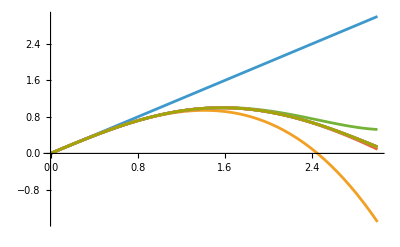

```mathematica
Plot[funzioni, {x, 0, 3}, PlotRange -> All]
```

```mathematica
Normal[Series[Gamma[x],{x,0,2}]]
```

-EulerGamma+1/x+1/12 (6 EulerGamma^2+π^2) x+1/6 x^2 (-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])

```mathematica
Plot3D[ {Re[Gamma[x+I y]], Im[Gamma[x+I y]]}, {x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[phi] Cos[th], Sin[phi] Sin[th], Cos[phi]}, {phi, 0, Pi}, {th, 0, 2 Pi}]
```

-Graphics3D-

```mathematica
comm[m1_, m2_] := m1.m2 - m2.m1 (*le variabili di input di una funzione sono dichiarate con un "_" finale*)
(*definiamo le Matrici di Pauli*)
s[1] := { {0,1}, {1,0}}
s[2] := {{0,-I}, {I, 0}}
s[3] := {{1, 0}, {0, -1}}
```

```mathematica
(*creiamo una tabella che ci verifichi tutte e 9 le possibili relazioni di commutazione tra le Matrici di Pauli*)
Table[comm[s[i],s[j]] === 2 I Sum[Signature[{i, j, k}] s[k],{k, 1, 3}], {i, 1, 3}, {j, 1, 3}]
```

{{True,True,True},{True,True,True},{True,True,True}}

```mathematica
ggg[b,a]
```

ggg[a,b]

```mathematica
SetAttributes[ggg, Orderless]
ggg[b,a]
```

ggg[a,b]

```mathematica
x = 3
```

3

```mathematica
f[x_] = a x^2 + b
```

9 a+b

```mathematica
g[x_] := a x^2 + b
g[y]
```

b+a y^2

```mathematica
MatchQ[x^2, _^_] (*funzione che restituisce una variale booleana True o False a seconda che l'espressione al primo argomento matchi formalmente quella al secondo*)
```

True

```mathematica
Clear[x]
prova := a x^3 + b x^2 + c x + d
prova /. {_^_ -> pippo} (*mettendo _^_. il comando ritorna solo 'pippo'*)
```

d+a pippo+b pippo+c x

```mathematica
(* riordino di operatori di creazione e distruzione:
"a adagger a" deve diventare "adagger a a + a" *)

h[x___,a,adagger,y___] := h[x,adagger,a,y] + h[x,y]

(*Questa riga definisce una regola di riscrittura ricorsiva per la funzione h,utilizzando il pattern matching in Mathematica

'x___' e 'y___' indicano rispettivamente 'zero o più elementi prima di a' e 'zero più elementi dopo di adagger'*)

h[a, adagger, a]
```

h[a]+h[adagger,a,a]

```mathematica
prova2 = (x-3) (x^2 + 4) ( x+x^2)
```

(-3+x) (4+x^2) (x+x^2)

```mathematica
Simplify[%212]
```

(-3+x) x (1+x) (4+x^2)

```mathematica
(* integrale di un polinomio *)
```